# Schwarzchild (d=4)

```mathematica
SetOptions[Plot,BaseStyle->{Thickness[0.005],FontFamily->"Times",FontSize->15}];
SetOptions[ListPlot,BaseStyle->{FontFamily->"Times",FontSize->20}];
SetOptions[Plot3D,BaseStyle->{FontFamily->"Times",FontSize->20}];
```

## Generalties

```mathematica
ClearAll;
```

```mathematica
Quit[]
```

For Sch BH, the metric has the next blackening factor

```mathematica
f[r_,m_]=1-(2 m)/r;
```

```mathematica
Mass[r_]=m/.Solve[f[r,m]==0,m]//Last
```

r/2

the surface gravity is

```mathematica
κappa[r_]=1/2(D[f[r,m], r])/.m->Mass[r]
```

1/(2 r)

the temperature is given by T=κ/(2 π)

```mathematica
Temp[r_]=κappa[r]/(2 π)
```

1/(4 π r)

now, we check that it satisfy the First Law and Smarr relation. We define the thermodynamics quantities as

```mathematica
Mfunr[r_]=r/2;
Tfunr[r_]=1/(4 π r);
Sfunr[r_]= π r^2;
```

Then, the Smarr relation

```mathematica
Mfunr[r]-2 Sfunr[r] Tfunr[r]
```

0

as we expected. And the First Law dM = TdS, thus

```mathematica
Dt[Mfunr[r]]-Tfunr[r]Dt[Sfunr[r]]
```

0

as we expected too.

## Free energy and Heat Capaticy

Now we want to compute the Helmhotlz Free energy F=E-TS, where in BH Thermo, the integral energy is the BH mass, then

```mathematica
rfunT[T_]=r/.Solve[Tfunr[r]==T,r]//Last
```

1/(4 π T)

```mathematica
SfunT[T_]=Sfunr[rfunT[T]]
```

1/(16 π T^2)

```mathematica
FreeEnergyFfunr[r_]=Mfunr[r]-Tfunr[r]Sfunr[r]
```

r/4

```mathematica
FreeEnergyFfunT[T_]=FreeEnergyFfunr[rfunT[T]]
```

1/(16 π T)

then for the heat capacity C_P=T*(∂S)/(∂T) we can express the entropy in terms of temperature, therefore

```mathematica
HeatCapacityCPfunT[T_]=T*D[SfunT[T], T]
```

-1/(8 π T^2)

```mathematica
HeatCapacityCPfunr[r_]=HeatCapacityCPfunT[Tfunr[r]]
```

-2 π r^2

Now we plot, the Hemholtz Free energy vs T

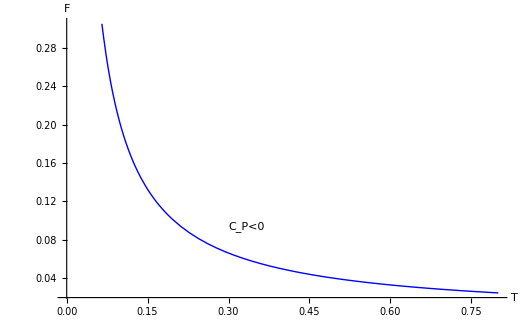

```mathematica
Plot[FreeEnergyFfunT[T],{T,0,0.8},AxesLabel->{"T","F"},PlotStyle->Blue,Epilog->{Text["C_P<0",{0.3,0.1},{-2,1}]}]
```

```mathematica
Export["C:\\Users\\Xiomara (ADMIN)\\Desktop\\Pandaza\\Archivos del dropbox\\Proyecto P Bueno\\BH Ext Thermo no-shared\\FreeEnergy_Schw.pdf",Plot[FreeEnergyFfunT[T],{T,0,0.8},AxesLabel->{"T","F"},PlotStyle->Blue,Epilog->{Text["C_P<0",{0.3,0.1},{-2,1}]}]]
```

C:\Users\Xiomara (ADMIN)\Desktop\Pandaza\Archivos del dropbox\Proyecto P Bueno\BH Ext Thermo no-shared\FreeEnergy_Schw.pdf

and the Heat Capacity vs T

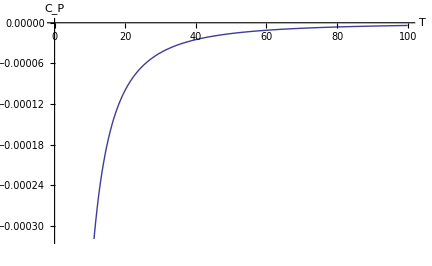

```mathematica
Plot[HeatCapacityCPfunT[T],{T,0,100},AxesLabel->{"T","C_P"}]
```

```mathematica
Export["C:\\Users\\Xiomara (ADMIN)\\Desktop\\Pandaza\\Archivos del dropbox\\Proyecto P Bueno\\BH Ext Thermo no-shared\\HeatCap_Schw.pdf",Plot[HeatCapacityCPfunT[T],{T,0,100},AxesLabel->{"T","C_P"},PlotStyle->Blue]]
```

C:\Users\Xiomara (ADMIN)\Desktop\Pandaza\Archivos del dropbox\Proyecto P Bueno\BH Ext Thermo no-shared\HeatCap_Schw.pdf

# Reissner-Nordstrom (d=4)

```mathematica
SetOptions[Plot,BaseStyle->{Thickness[0.005],FontFamily->"Times",FontSize->15}];
SetOptions[ListPlot,BaseStyle->{FontFamily->"Times",FontSize->20}];
SetOptions[Plot3D,BaseStyle->{FontFamily->"Times",FontSize->20}];
```

## Generalties

```mathematica
Quit[]
```

For Sch BH, the metric has the next blackening factor

```mathematica
f[r_,m_,Q_]=1-(2 m)/r+Q^2/r^2;
```

```mathematica
Mass[r_,Q_]=m/.Solve[f[r,m,Q]==0,m]//Last
```

(Q^2+r^2)/(2 r)

```mathematica
kappa[r_,Q_]=1/2 D[f[r,m,Q], r]/.m->Mass[r,Q]//Simplify
```

(-Q^2+r^2)/(2 r^3)

```mathematica
Temp[r_,Q_]=kappa[r,Q]/(2 π)
```

(-Q^2+r^2)/(4 π r^3)

Now, we can write the Thermodynamics

```mathematica
MfunrQ[r_,Q_]=(Q^2+r^2)/(2 r);
TfunrQ[r_,Q_]=(-Q^2+r^2)/(4 π r^3);
Sfunr[r_]=π r^2;
ΦfunrQ[r_,Q_]=Q/r;
```

Therefore the Smarr relation

```mathematica
MfunrQ[r,Q]-(2 TfunrQ[r,Q]Sfunr[r]+ΦfunrQ[r,Q]Q)//Simplify
```

0

closed as we expected.

Thus, the First Law

```mathematica
Dt[MfunrQ[r,Q]] -(TfunrQ[r,Q]Dt[Sfunr[r]]+ΦfunrQ[r,Q]Dt[Q])//Simplify
```

0

also close as we expected.

## Free Energy and Heat Capacity

Also we can compute the Free energy F, but we can express “r” as function of temperature and charge

```mathematica
Solve[TfunrQ[r,Q]==T,r]//Simplify
```

{{r→(2-2/((-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))-2 (-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))/(24 π T)},{r→(4+(2+2 ⅈ √3)/((-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))+2 (1-ⅈ √3) (-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))/(48 π T)},{r→(4+(2-2 ⅈ √3)/((-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))+2 (1+ⅈ √3) (-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))/(48 π T)}}

```mathematica
Solve[TfunrQ[r,Q]==T,r][[2]]//Simplify
```

{r→(4+(2+2 ⅈ √3)/((-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))+2 (1-ⅈ √3) (-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))/(48 π T)}

we can identified three roots of “r”, therefore we can plot this for Q fix in free energy

```mathematica
FreeEnergyFfunrQ[r_,Q_]=MfunrQ[r,Q]-TfunrQ[r,Q]Sfunr[r]//Simplify
```

(3 Q^2+r^2)/(4 r)

```mathematica
FreeEnergyfunTQ1[T_,Q_]=FreeEnergyFfunrQ[r,Q]/.Solve[TfunrQ[r,Q]==T,r][[1]]//Simplify
FreeEnergyfunTQ2[T_,Q_]=FreeEnergyFfunrQ[r,Q]/.Solve[TfunrQ[r,Q]==T,r][[2]]//Simplify
FreeEnergyfunTQ3[T_,Q_]=FreeEnergyFfunrQ[r,Q]/.Solve[TfunrQ[r,Q]==T,r][[3]]//Simplify
```

(6 π T (3 Q^2+((-2+2/((-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))+2 (-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))^2)/(576 π^2 T^2)))/(2-2/((-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))-2 (-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))

(12 π T (3 Q^2+((4+(2+2 ⅈ √3)/((-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))+2 (1-ⅈ √3) (-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))^2)/(2304 π^2 T^2)))/(4+(2+2 ⅈ √3)/((-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))+2 (1-ⅈ √3) (-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))

(12 π T (3 Q^2+((4+(2-2 ⅈ √3)/((-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))+2 (1+ⅈ √3) (-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))^2)/(2304 π^2 T^2)))/(4+(2-2 ⅈ √3)/((-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))+2 (1+ⅈ √3) (-1+216 π^2 Q^2 T^2+12 π √(-3 Q^2 T^2+324 π^2 Q^4 T^4))^(1/3))

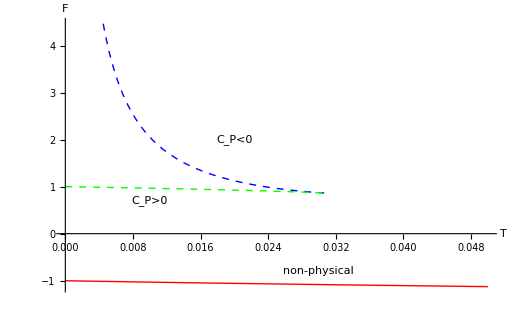

```mathematica
Plot[{FreeEnergyfunTQ1[T,1],FreeEnergyfunTQ2[T,1],FreeEnergyfunTQ3[T,1]},{T,0,0.05},PlotStyle->{Red,{Dashed,Blue},{Dashed,Green}},AxesLabel->{"T","F"},Epilog->{Text["C_P>0",{0.01,0.7},{-0,0}],Text["C_P<0",{0.02,2},{-0,0}],Text["non-physical",{0.03,-0.8},{-0,0}]}]
```

```mathematica
Export["C:\\Users\\Xiomara (ADMIN)\\Desktop\\Pandaza\\Archivos del dropbox\\Proyecto P Bueno\\BH Ext Thermo no-shared\\FreeEnergy_RN.pdf",Plot[{FreeEnergyfunTQ1[T,1],FreeEnergyfunTQ2[T,1],FreeEnergyfunTQ3[T,1]},{T,0,0.05},PlotStyle->{Red,{Dashed,Blue},{Dashed,Green}},AxesLabel->{"T","F"},Epilog->{Text["C_P>0",{0.01,0.7},{-0,0}],Text["C_P<0",{0.02,2},{-0,0}],Text["non-physical",{0.03,-0.8},{-0,0}]}]]
```

C:\Users\Xiomara (ADMIN)\Desktop\Pandaza\Archivos del dropbox\Proyecto P Bueno\BH Ext Thermo no-shared\FreeEnergy_RN.pdf

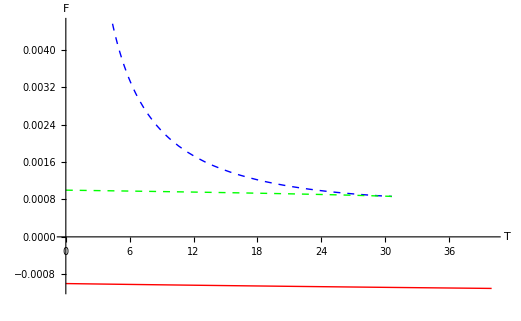

```mathematica
Plot[{FreeEnergyfunTQ1[T,0.001],FreeEnergyfunTQ2[T,0.001],FreeEnergyfunTQ3[T,0.001]},{T,0,40},PlotStyle->{Red,{Dashed,Blue},{Dashed,Green}},AxesLabel->{"T","F"}]
```

```mathematica
HeatCapacityCPfunrQ[r_,Q_]=TfunrQ[r,Q]D[Sfunr[r], r]*(D[TfunrQ[r,Q], r])^-1//Simplify
```

-(2 π r^2 (-Q^2+r^2))/(-3 Q^2+r^2)

```mathematica
HeatCapacityCPfunTQ1[T_,Q_]=HeatCapacityCPfunrQ[r,Q]/.Solve[TfunrQ[r,Q]==T,r][[1]]
HeatCapacityCPfunTQ2[T_,Q_]=HeatCapacityCPfunrQ[r,Q]/.Solve[TfunrQ[r,Q]==T,r][[2]]
HeatCapacityCPfunTQ3[T_,Q_]=HeatCapacityCPfunrQ[r,Q]/.Solve[TfunrQ[r,Q]==T,r][[3]]
```

-(2 π (1/(12 π T)-1/(6 2^(2/3) π T (-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))-((-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))/(12 2^(1/3) π T))^2 (-Q^2+(1/(12 π T)-1/(6 2^(2/3) π T (-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))-((-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))/(12 2^(1/3) π T))^2))/(-3 Q^2+(1/(12 π T)-1/(6 2^(2/3) π T (-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))-((-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))/(12 2^(1/3) π T))^2)

-(2 π (1/(12 π T)+(1+ⅈ √3)/(12 2^(2/3) π T (-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))+((1-ⅈ √3) (-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))/(24 2^(1/3) π T))^2 (-Q^2+(1/(12 π T)+(1+ⅈ √3)/(12 2^(2/3) π T (-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))+((1-ⅈ √3) (-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))/(24 2^(1/3) π T))^2))/(-3 Q^2+(1/(12 π T)+(1+ⅈ √3)/(12 2^(2/3) π T (-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))+((1-ⅈ √3) (-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))/(24 2^(1/3) π T))^2)

-(2 π (1/(12 π T)+(1-ⅈ √3)/(12 2^(2/3) π T (-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))+((1+ⅈ √3) (-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))/(24 2^(1/3) π T))^2 (-Q^2+(1/(12 π T)+(1-ⅈ √3)/(12 2^(2/3) π T (-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))+((1+ⅈ √3) (-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))/(24 2^(1/3) π T))^2))/(-3 Q^2+(1/(12 π T)+(1-ⅈ √3)/(12 2^(2/3) π T (-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))+((1+ⅈ √3) (-2+432 π^2 Q^2 T^2+√(-4+(-2+432 π^2 Q^2 T^2)^2))^(1/3))/(24 2^(1/3) π T))^2)

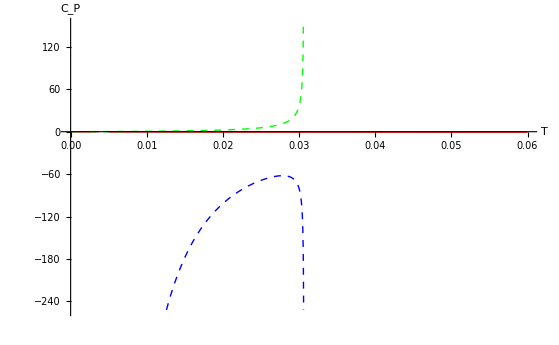

```mathematica
Plot[{HeatCapacityCPfunTQ1[T,1],HeatCapacityCPfunTQ2[T,1],HeatCapacityCPfunTQ3[T,1]},{T,0,0.06},PlotStyle->{Red,{Dashed,Blue},{Dashed,Green}},AxesLabel->{"T","C_P"}]
```

```mathematica
Export["C:\\Users\\Xiomara (ADMIN)\\Desktop\\Pandaza\\Archivos del dropbox\\Proyecto P Bueno\\BH Ext Thermo no-shared\\HeatCap_RN.pdf",Plot[{HeatCapacityCPfunTQ1[T,1],HeatCapacityCPfunTQ2[T,1],HeatCapacityCPfunTQ3[T,1]},{T,0,0.06},PlotStyle->{Red,{Dashed,Blue},{Dashed,Green}},AxesLabel->{"T","C_P"}]]
```

C:\Users\Xiomara (ADMIN)\Desktop\Pandaza\Archivos del dropbox\Proyecto P Bueno\BH Ext Thermo no-shared\HeatCap_RN.pdf

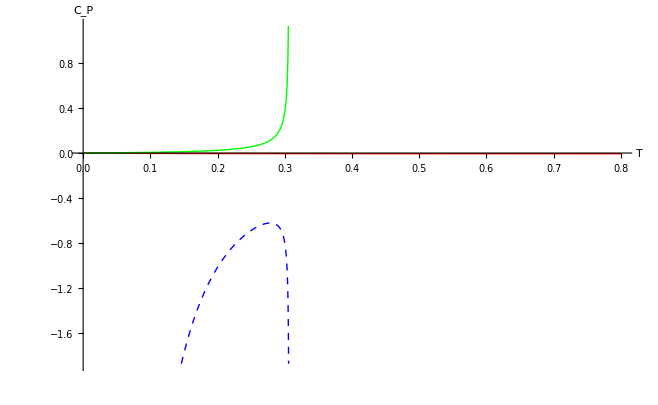

```mathematica
Plot[{HeatCapacityCPfunTQ1[T,0.1],HeatCapacityCPfunTQ2[T,0.1],HeatCapacityCPfunTQ3[T,0.1]},{T,0,0.8},PlotStyle->{Red,{Dashed,Blue},Green},AxesLabel->{"T","C_P"}]
```

```mathematica
HeatCapacityCPfunTQ1[T,0]//Simplify
```

0

```mathematica
HeatCapacityCPfunTQ2[T,0]//Simplify
```

-1/(8 π T^2)

```mathematica
HeatCapacityCPfunTQ3[T,0]//Simplify
```

0

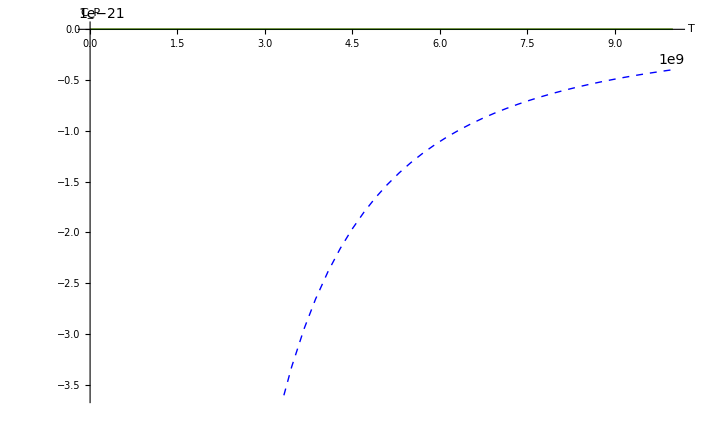

```mathematica
Plot[{HeatCapacityCPfunTQ1[T,0],HeatCapacityCPfunTQ2[T,0],HeatCapacityCPfunTQ3[T,0]},{T,0,10^10},PlotStyle->{Red,{Dashed,Blue},Green},AxesLabel->{"T","C_P"}]
```

# Kerr (d=4)

```mathematica
SetOptions[Plot,BaseStyle->{Thickness[0.005],FontFamily->"Times",FontSize->20}];
SetOptions[ListPlot,BaseStyle->{FontFamily->"Times",FontSize->20}];
SetOptions[Plot3D,BaseStyle->{FontFamily->"Times",FontSize->20}];
```

## Generalties

```mathematica
Quit[]
```

For Sch BH, the metric has the next blackening factor

```mathematica
f[r_,m_,Q_]=1-(2 m)/r+Q^2/r^2;
```

```mathematica
Mass[r_,Q_]=m/.Solve[f[r,m,Q]==0,m]//Last
```

(Q^2+r^2)/(2 r)

```mathematica
kappa[r_,Q_]=1/2 D[f[r,m,Q], r]/.m->Mass[r,Q]//Simplify
```

(-Q^2+r^2)/(2 r^3)

```mathematica
Temp[r_,Q_]=kappa[r,Q]/(2 π)
```

(-Q^2+r^2)/(4 π r^3)

Now, we can write the Thermodynamics

```mathematica
Mfunra[r_,a_]=(a^2+r^2)/(2 r);
Tfunra[r_,a_]=1/(2 π)(r/(r^2+a^2)-1/(2 r));
Sfunra[r_,a_]=π( r^2+a^2);
Jfunra[r_,a_]=a/(2r)(a^2+r^2);
Ωfunra[r_,a_]=a/(r^2+a^2);
```

Therefore the Smarr relation

```mathematica
Mfunra[r,a]-(2 Tfunra[r,a]Sfunra[r,a]+2 Ωfunra[r,a]Jfunra[r,a])//Simplify
```

0

closed as we expected.

Thus, the First Law

```mathematica
Dt[Mfunra[r,a]] -(Tfunra[r,a]Dt[Sfunra[r,a]]+Ωfunra[r,a]Dt[Jfunra[r,a]])//Simplify
```

0

also close as we expected.

## Free Energy and Heat Capacity

Also we can compute the Free energy F, but we can express “r” as function of temperature and charge

```mathematica
Solve[Tfunra[r,a]==T,r]//Simplify
```

{{r→(1+(-1+48 a^2 π^2 T^2)/((-1+288 a^2 π^2 T^2+12 π √(-3 a^2 T^2+528 a^4 π^2 T^4+768 a^6 π^4 T^6))^(1/3))-(-1+288 a^2 π^2 T^2+12 π √(-3 a^2 T^2+528 a^4 π^2 T^4+768 a^6 π^4 T^6))^(1/3))/(12 π T)},{r→(2-(ⅈ (-ⅈ+√3) (-1+48 a^2 π^2 T^2))/((-1+288 a^2 π^2 T^2+12 π √(-3 a^2 T^2+528 a^4 π^2 T^4+768 a^6 π^4 T^6))^(1/3))+(1-ⅈ √3) (-1+288 a^2 π^2 T^2+12 π √(-3 a^2 T^2+528 a^4 π^2 T^4+768 a^6 π^4 T^6))^(1/3))/(24 π T)},{r→(2+(ⅈ (ⅈ+√3) (-1+48 a^2 π^2 T^2))/((-1+288 a^2 π^2 T^2+12 π √(-3 a^2 T^2+528 a^4 π^2 T^4+768 a^6 π^4 T^6))^(1/3))+(1+ⅈ √3) (-1+288 a^2 π^2 T^2+12 π √(-3 a^2 T^2+528 a^4 π^2 T^4+768 a^6 π^4 T^6))^(1/3))/(24 π T)}}

we can identified three roots of “r”, therefore we can plot this for Q fix in free energy

```mathematica
FreeEnergyFfunra[r_,a_]=Mfunra[r,a]-Tfunra[r,a]Sfunra[r,a]//Simplify
```

(3 a^2+r^2)/(4 r)

```mathematica
FreeEnergyfunTa1[T_,a_]=FreeEnergyFfunra[r,a]/.Solve[Tfunra[r,a]==T,r][[1]]
FreeEnergyfunTa2[T_,a_]=FreeEnergyFfunra[r,a]/.Solve[Tfunra[r,a]==T,r][[2]]
FreeEnergyfunTa3[T_,a_]=FreeEnergyFfunra[r,a]/.Solve[Tfunra[r,a]==T,r][[3]]
```

(3 a^2+(1/(12 π T)+(-1+48 a^2 π^2 T^2)/(12 π T (-1+288 a^2 π^2 T^2+12 √3 π √(-a^2 T^2+176 a^4 π^2 T^4+256 a^6 π^4 T^6))^(1/3))-((-1+288 a^2 π^2 T^2+12 √3 π √(-a^2 T^2+176 a^4 π^2 T^4+256 a^6 π^4 T^6))^(1/3))/(12 π T))^2)/(4 (1/(12 π T)+(-1+48 a^2 π^2 T^2)/(12 π T (-1+288 a^2 π^2 T^2+12 √3 π √(-a^2 T^2+176 a^4 π^2 T^4+256 a^6 π^4 T^6))^(1/3))-((-1+288 a^2 π^2 T^2+12 √3 π √(-a^2 T^2+176 a^4 π^2 T^4+256 a^6 π^4 T^6))^(1/3))/(12 π T)))

(3 a^2+(1/(12 π T)-((1+ⅈ √3) (-1+48 a^2 π^2 T^2))/(24 π T (-1+288 a^2 π^2 T^2+12 √3 π √(-a^2 T^2+176 a^4 π^2 T^4+256 a^6 π^4 T^6))^(1/3))+((1-ⅈ √3) (-1+288 a^2 π^2 T^2+12 √3 π √(-a^2 T^2+176 a^4 π^2 T^4+256 a^6 π^4 T^6))^(1/3))/(24 π T))^2)/(4 (1/(12 π T)-((1+ⅈ √3) (-1+48 a^2 π^2 T^2))/(24 π T (-1+288 a^2 π^2 T^2+12 √3 π √(-a^2 T^2+176 a^4 π^2 T^4+256 a^6 π^4 T^6))^(1/3))+((1-ⅈ √3) (-1+288 a^2 π^2 T^2+12 √3 π √(-a^2 T^2+176 a^4 π^2 T^4+256 a^6 π^4 T^6))^(1/3))/(24 π T)))

(3 a^2+(1/(12 π T)-((1-ⅈ √3) (-1+48 a^2 π^2 T^2))/(24 π T (-1+288 a^2 π^2 T^2+12 √3 π √(-a^2 T^2+176 a^4 π^2 T^4+256 a^6 π^4 T^6))^(1/3))+((1+ⅈ √3) (-1+288 a^2 π^2 T^2+12 √3 π √(-a^2 T^2+176 a^4 π^2 T^4+256 a^6 π^4 T^6))^(1/3))/(24 π T))^2)/(4 (1/(12 π T)-((1-ⅈ √3) (-1+48 a^2 π^2 T^2))/(24 π T (-1+288 a^2 π^2 T^2+12 √3 π √(-a^2 T^2+176 a^4 π^2 T^4+256 a^6 π^4 T^6))^(1/3))+((1+ⅈ √3) (-1+288 a^2 π^2 T^2+12 √3 π √(-a^2 T^2+176 a^4 π^2 T^4+256 a^6 π^4 T^6))^(1/3))/(24 π T)))

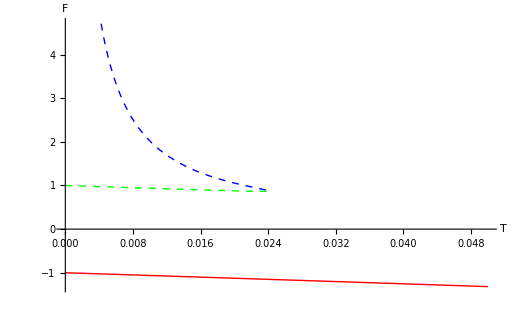

```mathematica
Plot[{FreeEnergyfunTa1[T,1],FreeEnergyfunTa2[T,1],FreeEnergyfunTa3[T,1]},{T,0,0.05},PlotStyle->{Red,{Dashed,Blue},{Dashed,Green}},AxesLabel->{"T","F"}]
```

```mathematica
Solve[Tfunra[r,a]==T,a]
```

{{a→-(r √(-1+4 π r T))/(√(-1-4 π r T))},{a→(r √(-1+4 π r T))/(√(-1-4 π r T))}}

```mathematica
Sfunra[r,√x]/.{x->-(r^2 (-1+4 π r T))/(1+4 π r T)}//Simplify
```

(2 π r^2)/(1+4 π r T)

```mathematica
HeatCapacityCPfunra[r_,a_]=Tfunra[r,a]*(D[Sfunra[r,a], r](D[Tfunra[r,a], r])^-1)//ExpandAll//Simplify
```

(2 π r^2 (a^4-r^4))/(-a^4-4 a^2 r^2+r^4)

```mathematica
-(8 π^2 r^3 T)/(1+4 π r T)^2/.T->Tfunra[r,a]//Simplify
```

(π (a^4-r^4))/(2 r^2)

```mathematica
HeatCapacityCPfunra[r,0]
```

-2 π r^2

```mathematica
HeatCapacityCPfunTQ1[T_,Q_]=HeatCapacityCPfunrQ[r,Q]/.Solve[TfunrQ[r,Q]==T,r][[1]]//FullSimplify
HeatCapacityCPfunTQ2[T_,Q_]=HeatCapacityCPfunrQ[r,Q]/.Solve[TfunrQ[r,Q]==T,r][[2]]//FullSimplify
HeatCapacityCPfunTQ3[T_,Q_]=HeatCapacityCPfunrQ[r,Q]/.Solve[TfunrQ[r,Q]==T,r][[3]]//FullSimplify
```

-((-1+1/((-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))+(-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))^2 (-Q^2+((-1+1/((-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))+(-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))^2)/(144 π^2 T^2)))/(72 π T^2 (-3 Q^2+((-1+1/((-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))+(-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))^2)/(144 π^2 T^2)))

-((4+(2+2 ⅈ √3)/((-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))+2 (1-ⅈ √3) (-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))^2 (-Q^2+((4+(2+2 ⅈ √3)/((-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))+2 (1-ⅈ √3) (-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))^2)/(2304 π^2 T^2)))/(1152 π T^2 (-3 Q^2+((4+(2+2 ⅈ √3)/((-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))+2 (1-ⅈ √3) (-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))^2)/(2304 π^2 T^2)))

-((4+(2-2 ⅈ √3)/((-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))+2 (1+ⅈ √3) (-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))^2 (-Q^2+((4+(2-2 ⅈ √3)/((-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))+2 (1+ⅈ √3) (-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))^2)/(2304 π^2 T^2)))/(1152 π T^2 (-3 Q^2+((4+(2-2 ⅈ √3)/((-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))+2 (1+ⅈ √3) (-1+12 π (18 π Q^2 T^2+√(-3 Q^2 T^2+324 π^2 Q^4 T^4)))^(1/3))^2)/(2304 π^2 T^2)))

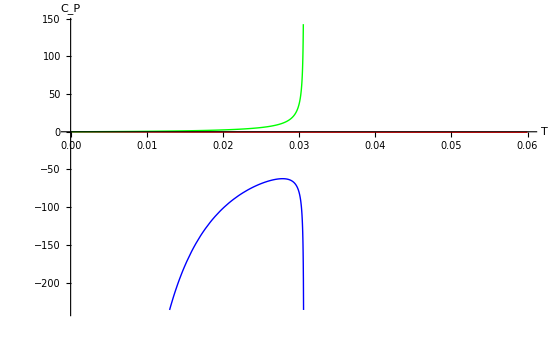

```mathematica
Plot[{HeatCapacityCPfunTQ1[T,1],HeatCapacityCPfunTQ2[T,1],HeatCapacityCPfunTQ3[T,1]},{T,0,0.06},PlotStyle->{Red,Blue,Green},AxesLabel->{"T","C_P"}]
```

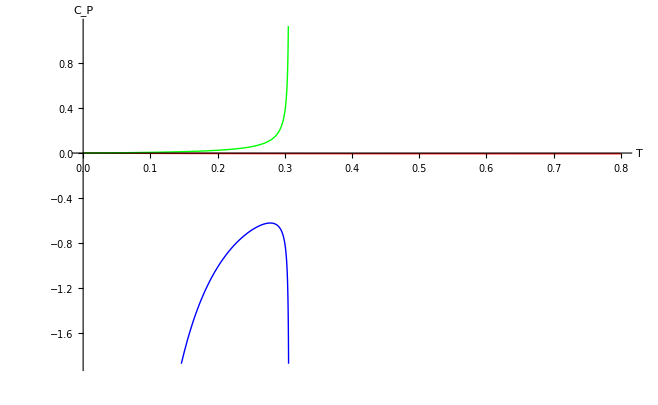

```mathematica
Plot[{HeatCapacityCPfunTQ1[T,0.1],HeatCapacityCPfunTQ2[T,0.1],HeatCapacityCPfunTQ3[T,0.1]},{T,0,0.8},PlotStyle->{Red,Blue,Green},AxesLabel->{"T","C_P"}]
```

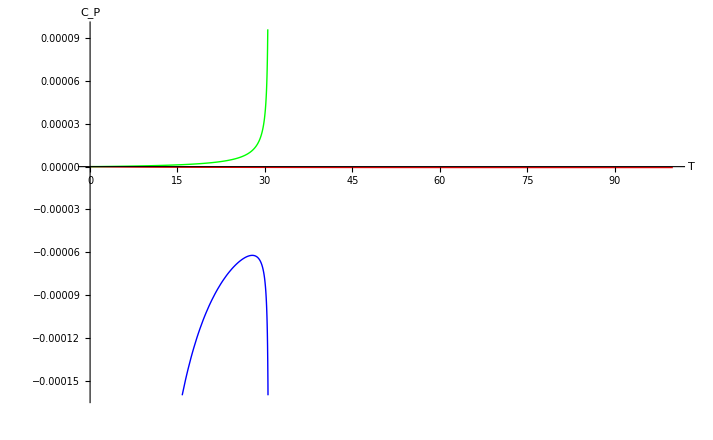

```mathematica
Plot[{HeatCapacityCPfunTQ1[T,0.001],HeatCapacityCPfunTQ2[T,0.001],HeatCapacityCPfunTQ3[T,0.001]},{T,0,100},PlotStyle->{Red,Blue,Green},AxesLabel->{"T","C_P"}]
```